# Математические основы защиты информации Лабораторная работа №4 Эллиптические кривые

БГУ, ММФ, Каф. ДУиСА, 
 доцент Чергинец Д.Н.

## Эллиптические кривые

Пусть K – поле действительных чисел или ℤ_p,  p>3 – простое, a,b∈K.  Эллиптической кривой ℰ(K) над полем K  называется множество точек (x,y)∈K^2, удовлетворяющих равенству
   
      y^2=x^3+a x+b,
также к эллиптической кривой добавляют бесконечно удаленную точку O.
Будем считать, что бесконечно удаленная точка принадлежит всем вертикальным прямым и не принадлежит невертикальным. 

Пусть F(x,y):=x^3+a x+b-y^2. 

Согласно теореме о неявной функции, если
F(x_0,y_0)=0,
(∂F)/(∂x)(x_0,y_0)≠0,
то в некоторой окрестности точки (x_0,y_0) уравнение F(x_0,y_0)=0 эквивалентно уравнению x=x(y).

А если
F(x_0,y_0)=0,
(∂F)/(∂y)(x_0,y_0)≠0,
то в некоторой окрестности точки (x_0,y_0) уравнение F(x_0,y_0)=0 эквивалентно уравнению y=y(x).

Найдем точки эллиптической кривой, в которых нарушаются условия теоремы о неявной функции.

F(x,y)=0,
(∂F)/(∂x)(x,y)=0
(∂F)/(∂y)(x,y)=0,             ⇔           x^3+a x+b-y^2==0,
3 x^2+a=0,
2y=0,          ⇔           ±√(-a/3)(-a/3+a) +b==0,
x=±√(-a/3),
y=0,    ⇔           b=∓2/3a √(-a/3);
x=±√(-a/3),
y=0, 

Если параметры кривой удовлетворяют условию
b=-2/3a √(-a/3)   или  b=2/3 a √(-a/3)        то   найдется точка, в которой не выполняются условия теоремы о неявной функции.
Условие   b=-2/3a √(-a/3)   или  b=2/3 a √(-a/3)      эквивалентно 4 a^3+27 b^2=0.
Величина D=4 a^3+27 b^2 называется дискриминантом эллиптической кривой. В криптографии рассматривают эллиптические кривые с D≠0.

### Задание 1.

Построить три эллиптические кривые ℰ(ℝ) для случаев D>0, D=0, D<0.

Для криптографии интересен случай K=ℤ_p.    Так как ℤ_p – конечное поле, то и ℰ(ℤ_p)  конечно.

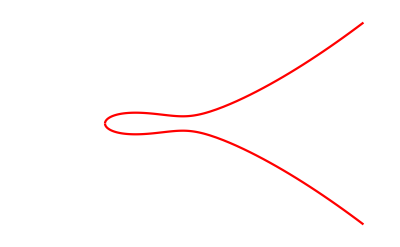
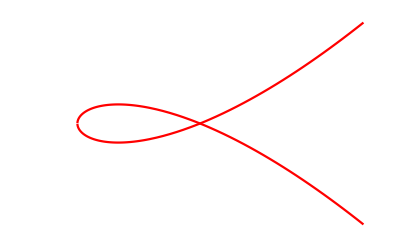
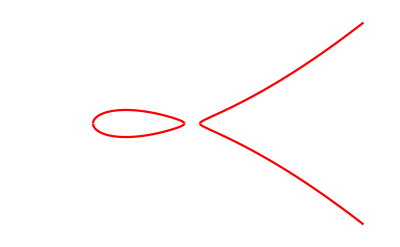
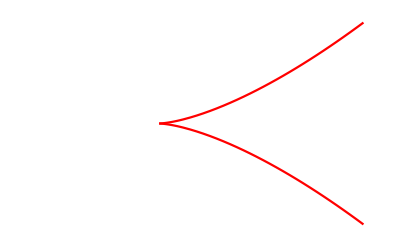

```mathematica
Plot[{√(x^3+#[[1]]*x+#[[2]]),-√(x^3+#[[1]]*x+#[[2]])},{x,-3,5},Axes->None,PlotStyle->{Red,Red}]&/@{{-1,1},{-3,2},{-2,1},{0,0}}
```

### Задание 2.

Реализовать функцию, которая вычисляет все точки эллиптической кривой ℰ(ℤ_p)  двумя способами:
- методом полного перебора;
- при помощи алгоритма Шенкса, изученного в прошлом семестре.
Сравнить время вычисления.

```mathematica
ClearAll[Curve]
DD[a_,b_]:=27*b^2+4*a^3
Curve[a_,b_,p_]:=Mod[PowerMod[#[[1]],3,p]+Mod[a*#[[1]],p]+b-PowerMod[#[[2]],2,p],p]&;
Curve[a_,b_,p_,"r"]:=Mod[PowerMod[#,3,p]+Mod[a*#,p]+b,p]&;
```

```mathematica
Curve[2,3,7,"r"][4]
```

5

### перебор

```mathematica
BruteForce[a_,b_,p_]:=Block[{i,j,res={{None,None}}},For[i=0,i<p,i++,For[j=0,j<p,j++,If[Curve[a,b,p][{i,j}]==0,AppendTo[res,{i,j}]]]];res]
```

```mathematica
BruteForce[2,3,7]
Curve[2,3,7]/@Rest@%
```

{{None,None},{2,1},{2,6},{3,1},{3,6},{6,0}}

{0,0,0,0,0}

### шенкс

```mathematica
ClearAll[FindN];
FindN[p_]:=Block[{n=RandomInteger[p]},While[PowerMod[n,(p-1)/2,p]!=p-1,n=RandomInteger[p]];n]
```

```mathematica
ClearAll[shenks];
shenks[a_,p_]:=Block[{s= IntegerExponent[p-1,2],t,n=FindN[p],b,r,d=0,f,c,x,i},t=(p-1)/2^s;b=PowerMod[n,t,p];r=PowerMod[a,(t+1)/2,p];f=PowerMod[a,t,p];c=b;For[i=1,i<s,i++,c=PowerMod[c,2,p];If[PowerMod[f,2*s-1-i,p]!=1,d+=2^i;f=Mod[f*c,p]]];x=Mod[r*PowerMod[b,d/2,p],p];Return@If[PowerMod[x,2,p]==a,x,None]]
```

```mathematica
ClearAll[shenksForCurve]
shenksForCurve[a_,b_,p_]:=Block[{i,tmp,res={{None,None}}},For[i=0,i<p,i++,tmp=shenks[Curve[a,b,p,"r"][i],p];If[FreeQ[tmp,None],AppendTo[res,{i,tmp}];AppendTo[res,{i,Mod[p-tmp,p]}]]];Return@DeleteDuplicates@res]
```

```mathematica
shenksForCurve[2,3,7]
```

{{None,None},{2,1},{2,6},{3,1},{3,6},{6,0}}

```mathematica
shenksForCurve[-2,1,11]
```

{{None,None},{0,1},{0,10},{1,0},{2,4},{2,7},{3,0},{7,0}}

### Сравнение

```mathematica
L=11;
p=RandomPrime[{2^(L-1),2^L}];
a=10;
b=21;
AbsoluteTiming[BruteForce[a,b,p];]
AbsoluteTiming[shenksForCurve[a,b,p];]
```

{19.1795,Null}

{0.0876365,Null}

Теорема.
Любая прямая, пересекающая эллиптическую кривую ℰ(K)  в двух точках, пересекает ℰ(K)  в третьей точке с учетом кратности точек. Более строго теорема выглядит следующим образом.

В случае невертикальной прямой для каждой пары  P_1=(x_1,y_1), P_2=(x_2,y_2)∈ℰ(K)   прямая  y=λ(x-x_1)+y_1,  где  λ=(y_2-y_1)/(x_2-x_1)  при  x_1≠x_2  или  λ=(3 x_1^2+a)/(2 y_1)  при  x_1=x_2,   y_1=y_2≠0 (случай касательной),  пересекает  ℰ(K)  в точке  P_3=(x_3,λ(x_3-x_1)+y_1).  Причем кубическое   уравнение
      (λ(x-x_1)+y_1)^2=x^3+a x+b
имеет три корня  x_1,x_2,x_3=λ^2-x_1-x_2. 

Для вертикальной прямой возможны лишь два случая.
1) Прямая пересекает точки  (x,y),   (x,-y),   O. 
2) Прямая пересекает точку   O. 

Определение. Пусть  K=ℝ  или  K=ℤ_p.  Операцию вычисления обратного  -P  определим следующими правилами: если  P=O,  то  -O=O,  иначе  -(x,y)=(x,-y). 

Определим операцию сложения  +:ℰ^2→ℰ.  Пусть  P_1,P_2∈ℰ,  тогда
              P_1+P_2=-P_3,
 где  P_3  – точка пересечения кривой  ℰ  с прямой, проходящей через точки  P_1,P_2.  В случае  P_1=P_2=O  будем считать, что  O+O=O.  Согласно данному определению имеем следующие формулы.
    1. Если  одна из точек бесконечно удаленная, то
            P+O=O+P=-(-P)=P.
Пусть далее  P_1,P_2  являются конечными и имеют координаты  P_1=(x_1,y_1),   P_2=(x_2,y_2). 
   2. Если  x_1=x_2,  y_1≠y_2,  то  P_1+P_2=O. 
   3. Если  x_1≠x_2,  то  x_3=λ^2-x_1-x_2, y_3=λ(x_1-x_3)-y_1,   λ=(y_2-y_1)/(x_2-x_1).    
   4. Если  x_1=x_2,   y_1=y_2≠0,  то  x_3=λ^2-x_1-x_2, y_3=λ(x_1-x_3)-y_1,   λ=(3 x_1^2+a)/(2 y_1).    
   5. Если   x_1=x_2,   y_1=y_2=0,  то  P+Q=O.

### Задание 3.

Реализовать функцию сложения в ℰ(ℤ_p).

Теорема.
  Эллиптическая кривая над полем 𝕂 с операцией сложения, заданной выше, является аддитивной абелевой группой при D≠0.

```mathematica
PlusCurve[p1_,p2_,a_,p_]:=Block[{x1,x2,y1,y2,λ,x3},If[MemberQ[p1,None] && MemberQ[p2,None],Return[{None,None}]];
If[MemberQ[p1,None] && FreeQ[p2,None],Return[p2]];
If[FreeQ[p1,None] && MemberQ[p2,None],Return[p1]];
{x1,y1}=p1;
{x2,y2}=p2;
If[x1==x2&&y1!=y2,Return[{None,None}]];
If[x1!=x2,λ=Mod[ModularInverse[x2-x1,p]*(y2-y1),p];x3=Mod[λ^2-x1-x2,p];Return[{x3,Mod[λ*(x1-x3)-y1,p]}]];
If[x1==x2&&(y1==y2!=0),λ=Mod[ModularInverse[2*y1,p]*3*x1^2+a,p];x3=Mod[λ^2-x1-x2,p];Return[{x3,Mod[λ*(x1-x3)-y1,p]}]];
If[x1==x2&&(y1==y2==0),Return[{None,None}]];
]
```

### Задание 4.

Для эллиптических кривых ℰ_1 и ℰ_2 проверить свойство ассоциативности
            (P + Q) + R = P + (Q + R)

```mathematica
elpnts = shenksForCurve[a1,b1,p1];
l=Length[elpnts];
(*permtable=Flatten[Table[{elpnts[[i]],elpnts[[j]],elpnts[[k]]},{i,1,l},{j,1,l},{k,1,l}],2];*)
(*res = {PlusCurve[PlusCurve[#[[1]],#[[2]],a1,p1],#[[3]],a1,p1],PlusCurve[#[[1]],PlusCurve[#[[2]],#[[3]],a1,p1],a1,p1]}&/@permtable;*)
res[[Flatten@Position[(Hash[#[[1]]]==Hash[#[[2]]])&/@res,False]]]
```

{{{523,521},{282,292}},{{2,508},{567,431}},{{364,482},{562,397}},{{639,535},{595,296}},{{474,511},{251,205}},{{50,501},{9,327}},{{290,229},{75,145}},{{433,511},{272,523}},{{597,333},{174,103}},{{402,256},{380,492}},{{312,336},{522,118}},5466,{{190,262},{93,374}},{{150,579},{173,226}},{{9,38},{514,420}},{{586,258},{265,534}},{{18,634},{455,358}},{{377,155},{36,489}},{{398,508},{605,593}},{{380,5},{106,629}},{{30,370},{129,566}},{{623,410},{45,417}},{{477,21},{484,333}}}
 |  |  |  |

#### Вариант 4.

```mathematica
Subscript[ℰ, 1];
{a1,b1,p1}={631, 525, 641};
P1={39, 42};
Q1={542, 90};
R1={94, 212};
Subscript[ℰ, 2];
{a2,b2,p2}={-3, -2, 47};
P2={38, 46};
Q2={46, 0};
R2={46, 0};
```

```mathematica
DD[a1,b1]
elpnts = shenksForCurve[a1,b1,p1];
res = {PlusCurve[PlusCurve[#[[1]],#[[2]],a1,p1],#[[3]],a1,p1],PlusCurve[#[[1]],PlusCurve[#[[2]],#[[3]],a1,p1],a1,p1]}&/@{{P1,Q1,R1}};
res
```

1012400239

{{{36,152},{36,152}}}

```mathematica
DD[a2,b2]
elpnts = shenksForCurve[a2,b2,p2];
res = {PlusCurve[PlusCurve[#[[1]],#[[2]],a2,p2],#[[3]],a2,p2],PlusCurve[#[[1]],PlusCurve[#[[2]],#[[3]],a2,p2],a2,p2]}&/@{{P2,Q2,R2}};
res
```

0

{{{None,None},{38,46}}}

## Цикличность группы

Порядком группы называется количество элементов группы.
Порядком m  точки P  эллиптической кривой ℰ(ℤ_p) называется наименьшее натуральное число такое, что 
m P=(P+P+…+P)_(m раз)=O.
Каждая точа P∈ℰ(ℤ_p) порождает циклическую подгруппу
<P>:={P,2P,…,m P=0}.
Если <P> =ℰ(ℤ_p), то группа ℰ(ℤ_p) называется циклической, а точка P –  образующей.

### Задание 5.

```mathematica
orderOfCurve[pnt_,a_,b_,p_]:=Block[{res=1,newPnt=pnt},While[FreeQ[newPnt,None],newPnt = PlusCurve[newPnt,pnt,a,p];res++];res]
```

```mathematica
orderOfCurve[a_,b_,p_]:=Length[shenksForCurve[a,b,p]]
orderOfCurve[lst_List]:=Length[lst]
```

Найти порядок эллиптических кривых  ℰ_1, ℰ_2, ℰ_3. Что можно сказать о цикличности группы ℰ_3 исходя из ее порядка. Определить, являются ли циклическими группы ℰ_1, ℰ_2.

#### Вариант 4.

```mathematica
Subscript[ℰ, 1];
{a1,b1,p1}={25, 31, 47};
Subscript[ℰ, 2];
{a2,b2,p2}={38, 17, 43};
Subscript[ℰ, 3];
{a3,b3,p3}={1, 3, 17};
```

```mathematica
orderOfCurve[a1,b1,p1]
orderOfCurve[#,a1,b1,p1]&/@shenksForCurve[a1,b1,p1]
"-------------"
orderOfCurve[a2,b2,p2]
orderOfCurve[#,a2,b2,p2]&/@shenksForCurve[a2,b2,p2]
"-------------"
orderOfCurve[a3,b3,p3]
orderOfCurve[#,a3,b3,p3]&/@shenksForCurve[a3,b3,p3]
```

orderOfCurve[25,31,47]

{1,51,14,24,49,23,19,16,49,18,51,12,43,7,14,56,29,21,53,2,49,53,2,2,37,23,12,20,7,54,45,47,46,44,50,20}

-------------

orderOfCurve[38,17,43]

{1,53,18,13,51,53,6,15,55,43,36,52,5,4,3,26,9,39,20,38,8,43,26,42,51,43,38,45,26,2,11,48,16,36,23,34,24,43,3,21,50,18,43,13,49,17}

-------------

orderOfCurve[1,3,17]

{1,13,8,16,10}

```mathematica
shenksForCurve[a3,b3,p3]
```

{{None,None},{11,11},{11,6},{16,1},{16,16}}

## Проблема дискретного логарифма в группе точек эллиптической кривой

Алгоритм вычисления   d P∈ℰ(K).

Дано  d∈ℕ,   P∈ℰ(K). 
Необходимо найти  d P∈ℰ(K). 
1.  Представляем  d  в двоичной системе счисления
   d=d_0 2^r+d_1 2^(r-1)+…+d_(r-1)2+d_r,   d_0=1.
2.  Пусть  P_0=P.  Для  j=1,…,r  вычисляем  P_j 
     Если d_j=1, то P_j:=P_(j-1)+P_(j-1)+P,
                         иначе  P_j:=P_(j-1)+P_(j-1).
3.  Искомым элементом является  P_r. 


Определение.
Пусть  P∈ℰ(ℤ_p),   Q∈<P>.  Проблемой дискретного логарифма над эллиптической кривой называется проблема отыскания такого  k∈ℕ,  что  k P=Q.

### Задание 6.

Реализовать алгоритм вычисления d P∈ℰ(K). Проверить его работу сложением:
6P=P+P+P+P+P+P.

```mathematica
IntegerDigits[34,2].(2^Range[0,5])
```

34

```mathematica
MultCurve[d_,pnt_,a_,b_,p_]:=Block[{dd=Reverse@IntegerDigits[d,2],result={None,None},Q=pnt,i},
For[i=1,i<=Length[dd],i++,If[dd[[i]]==1,result=PlusCurve[result,Q,a,p]];Q=PlusCurve[Q,Q,a,p]];result]
```

```mathematica
shenksForCurve[a1,b1,p1][[3]]
```

{2,29}

```mathematica
P=shenksForCurve[a1,b1,p1][[3]];
MultCurve[#,P,a1,b1,p1]&/@Range[6]
NestList[PlusCurve[#,P,a1,p1]&,P,5]
```

{{2,29},{30,1},{16,32},{37,9},{16,26},{12,33}}

{{2,29},{30,1},{16,32},{36,4},{33,9},{40,41}}

```mathematica
P=shenksForCurve[a2,b2,p2][[3]];
MultCurve[#,P,a2,b2,p2]&/@Range[6]
NestList[PlusCurve[#,P,a2,p2]&,P,5]
```

{{0,19},{25,20},{33,33},{3,9},{32,16},{26,1}}

{{0,19},{25,20},{33,33},{24,6},{34,3},{18,35}}

```mathematica
P=shenksForCurve[a3,b3,p3][[3]];
MultCurve[#,P,a3,b3,p3]&/@Range[6]
NestList[PlusCurve[#,P,a3,p3]&,P,5]
```

{{11,11},{8,16},{14,11},{16,13},{16,4},{12,11}}

{{11,11},{8,16},{14,11},{9,6},{16,2},{15,3}}

### Задание 7.

Существует ли эллиптическая кривая с трехкратной точкой касания прямой? То есть найдется ли такая эллиптическая кривая y^2=x^3+a x+b  и касательная y=λ(x-x_1)+y_1, λ=(3 x_1^2+a)/(2 y_1), что
x_1=λ^2-x_1-x_1.